# Term Project

### Project Proposal

1. Our project will be to create a 3D simulation that models launching an object from the earth into space and plotting its trajectory, as well as the landing location, if it does land. We plan on starting with just a simulation of launching the object and it coming back to earth so we can understand how to represent the simplest form of projectile motion. When we finish this, we will consider how to launch the object in such a way that it will reach the point at which it would start orbiting the earth. We will then consider additional components in our calculations like air resistance, how long the force of thrust should be applied, how using fuel changes the situation (i.e. the mass of the object changes as fuel is expended), and other components that we haven’t yet accounted for. Our goal is to create a module that produces a 3D graph plotting the trajectory of the projectile around the earth given certain input parameters.

2. To start, we will split up the research into the components listed above. Nicolas will investigate the relationship between fuel consumption and force, while Jason will research how to treat air resistance considering the changing density of the atmosphere with altitude. Both of us will look into the formulas behind projectile motion and objects orbiting the earth because neither of us are completely familiar with those topics. The first major milestone will be to create a 2D graph of projectile motion. The second major milestone will be to create a 2D graph of orbital motion around the earth. From there, we will model the same situations in 3D. Finally, we will individually add in the components we were each responsible for researching (fuel consumption, air resistance).

3. Our project will require analysis in the following areas: projectile motion, orbital motion/mechanics, air resistance, and the relationship between the mass of the fuel and the thrust it can provide. We will need to thoroughly understand how to create 3D graphs in Mathematica. These graphs will probably require space curves. We will analyze how each of the “additional” components we consider (air resistance, fuel/mass relationship, etc) interact with the other components, if they do. We will also need to make sure that our graph clearly shows where the object is as a function of time.

4. Problems could arise if we mix up variables in our code or we don’t correctly incorporate certain factors, meaning we misunderstand how one component impacts the other components. An example of this would be forgetting to account for the change in mass of the object/rocket as fuel is used up to enable thrust against the force of gravity, which changes with distance from the earth. Many other important issues we will need to carefully address are related to the 3D graph. How will we make the graph a function of time instead of space? How will we represent unsuccessful orbital paths on the graph? Can we model several paths at once? How will we model the earth and objects hitting the surface of the earth? We will need to ensure that the scale of the graph is such that the graph is useful and readable.

### First Milestone

The first major milestone will be to create a 2D graph of projectile motion.

We would be animating one object which is the projectile. One axis would be the ground and the other axis would be the height above the ground. We are hoping for it to include the past positions of where the object was.

Module that produces animation of 2D motion of a propelled projectile:

```mathematica
twoStage[thrustx_,thrusty_,timeThrustApplied_,mass_]:=Module[{g=-9.8,force,acc,vel,posThrustStage,posFreefallStage,aircraft,t,timeToGround,thrustPlot,freefallPlot},
(*thrust stage*)
force={thrustx,thrusty+mass*g};
acc=force/mass;
vel[t_]={0,0}+Integrate[acc,t]; (*No initial velocity*)
posThrustStage[t_]={0,0}+Integrate[vel[t],t];

(*set up the parametric plot for thrust stage*)
thrustPlot=ParametricPlot[posThrustStage[t],{t,0,timeThrustApplied},PlotStyle->{Blue, Dashed}];

(*freefall stage*)
force={0,mass*g}; (*because the projectile is in freefall*) 
acc=force/mass;
vel[t_]=(vel[timeThrustApplied])+Integrate[acc,t];
posFreefallStage[t_]=(posThrustStage[timeThrustApplied])+Integrate[vel[t],t];

(*calculate the time it will take the projectile to reach the ground, where the y component of position is less than 0*)
timeToGround=t/.FindRoot[posFreefallStage[t][[2]]==0,{t,100}];
(*Current issue: how can we reliably find the positive root, not the negative one?*)

(*set up module to switch which position function is used based on t*)
aircraft[t_]:=Module[{},
If[t<=timeThrustApplied,posThrustStage[t],posFreefallStage[t-timeThrustApplied]]];

(*set up the parametric plot*)
freefallPlot=ParametricPlot[posFreefallStage[t],{t,0,timeToGround},PlotStyle->{Red, Dashed}];

(*Show the final plot*)
(*Show[{thrustPlot,freefallPlot},PlotRange->All,AxesLabel->{"x Position","y Position"},PlotLabel->StringForm["Time to ground: `` seconds",timeThrustApplied+timeToGround]]*)

(*show the animation*)
Animate[Show[thrustPlot,freefallPlot,Graphics[Point[aircraft[t]]],PlotRange->All,AxesLabel->{"x Position","y Position"},PlotLabel->StringForm["Time to ground: `` seconds",timeThrustApplied+timeToGround]],{t,0,timeThrustApplied+timeToGround}]
]
```

```mathematica
twoStage[7,120,5,10]
```

### Second Milestone

The second major milestone will be to create a 2D graph of orbital motion around the earth. 

Two objects will be animated, where one is the earth, which wouldn’t move. The second would be the rocket’s position. For this one, the plot will be on an {x,y} axis with the time factor changing. 

Module that produces a plot of projectile motion with constant gravitation

```mathematica
TwoStageOrbit[thrustx_,thrusty_,timeThrustApplied_,mass_]:=Module[{g,massEarth,radiusEarth,centerOfEarth,bigG,maxAirTime,r,forceGravitation,force,acc,vel,pos,t,closestToEarth,timeClosestToEarth,timeToGround,thrustPlot,freefallPlot,earthObject},

(*define constants*)
g=-9.8;
massEarth=16900*9.8;
radiusEarth=130;
centerOfEarth={0,0};
bigG=1;
maxAirTime=20; (*maxAirTime is maximum time we will let a projectile remain in the air before we declare it as "in orbit or lost"*)

(*set up expressions related to universal gravitation initially*)
r=centerOfEarth-{0,radiusEarth}; (*r is a vector from the projectile to the center of the earth. This is based on initial position*)
forceGravitation=r*(bigG*mass*massEarth/Norm[r]^3);(*initial force of gravitation at launch*)

(*thrust stage*)
force={thrustx,thrusty}+forceGravitation;
acc=force/mass;
vel={0,0}+Integrate[acc,t]; (*No initial velocity*)
pos={0,radiusEarth}+Integrate[vel,t];

(*set up expressions related to universal gravitation again*)
r=centerOfEarth-pos; (*r is a vector from the projectile to the center of the earth*)
forceGravitation=r*(bigG*mass*massEarth/Norm[r]^3);

Print[N[forceGravitation[[2]]/.t->8]];

(*set up the parametric plot for thrust stage*)
thrustPlot=ParametricPlot[pos,{t,0,timeThrustApplied},PlotStyle->{Red, Dashed}];

(*freefall stage*)
force=forceGravitation; (*because the projectile is in freefall*) 
acc=force/mass;
vel=(vel/.t->timeThrustApplied)+Integrate[acc,t];
pos=(pos/.t->timeThrustApplied)+Integrate[vel,t];

(*calculate the time it will take the projectile to reach the surface of the Earth*)
(*first, find a local minimum on (0, maxAirTime)*)
closestToEarth=NMinimize[{Norm[r],0<t<=maxAirTime},t,Method->"RandomSearch"]; (*finds the global min of Norm[n] beteween 0<t<maxAirTime*)
timeClosestToEarth=t/.closestToEarth[[2]];

(*if the closest the projectile gets is less than the radius of the Earth...*)
If[closestToEarth[[1]]<radiusEarth,
timeToGround=t/.NMinimize[{Abs[Norm[r]-radiusEarth],0<=t<=timeClosestToEarth},t][[2]], (*look for when the projectile hits the ground!*)
timeToGround=maxAirTime (*the projectile never hits the ground, so we set plot all of maxAirTime*)
];

(*set up the parametric plot*)
freefallPlot=ParametricPlot[pos,{t,0,timeToGround},PlotStyle->{Blue, Dashed}];

(*set up earth graphics object*)
earthObject=Graphics[{Darker[Green],Disk[centerOfEarth,radiusEarth]}];

(*Show the final plot*)
Show[{earthObject,thrustPlot,freefallPlot},Axes->True,PlotRange->All,AxesLabel->{"x Position","y Position"},PlotLabel->StringForm["Time to ground: `` seconds",timeThrustApplied+timeToGround]]
]

TwoStageOrbit[1,20,5,1]
```

Testing Piecewise functions

```mathematica
force=Piecewise[{{{2,2},t<5},{{0,-9.8},t>=5}}]
acceleration=force/2
velocity=Integrate[acceleration,t]
position=Integrate[velocity,t]
ParametricPlot[position,{t,0,9}]
force/.t->5
```

Create a version of Orbit using a piecewise function. Currently BROKEN

```mathematica
Orbit[thrustx_,thrusty_,timeThrustApplied_,mass_]:=Module[{g,massEarth,radiusEarth,centerOfEarth,bigG,r,maxAirTime,force,acc,vel,pos,t,closestToEarth,timeClosestToEarth,timeToGround,thrustPlot,freefallPlot,earthObject},
(*define constants*)
g=-9.8;
massEarth=100;
radiusEarth=70;
centerOfEarth={0,0};
bigG=10;
maxAirTime=20; (*maxAirTime is maximum time we will let a projectile remain in the air before we declare it as "in orbit or lost"*)

(*set up force as a piecewise function*) (*forceGravitation:=*)
force=Piecewise[{{{thrustx,thrusty+mass*g},t<=timeThrustApplied},{{0,mass*g},t>timeThrustApplied}}];
acc=force/mass;
vel=Integrate[acc,t]; (*No initial velocity*)
pos=Integrate[vel,t];
Print[(pos/.t->2)+{1,0}];
temp={1,0}+pos;
Print[temp/.t->2];

r:=centerOfEarth-pos; (*r is a vector from the projectile to the center of the earth*)

tempPlot=Plot[{Norm[r],radiusEarth},{t,0,15}];

(*calculate the time it will take the projectile to reach the surface of the Earth*)
(*first, find a local minimum that represents the closest the projectile gets to the center of the earth*)
closestToEarth=FindMinimum[{Norm[r],t>0},{t,maxAirTime}]; (*finds the first minimum value of r where t is between 0 and maxAirtime*)
timeClosestToEarth=t/.closestToEarth[[2]];

(*if the closest the projectile gets is less than the radius of the Earth...*)
If[closestToEarth[[1]]<radiusEarth,
timeToGround=t/.FindRoot[Norm[r]==radiusEarth,{t,timeClosestToEarth/2}], (*look for when the projectile hits the ground!*)
timeToGround=maxAirTime (*the projectile never hits the ground, so we set plot all of maxAirTime*)
];

(*set up the parametric plot for thrust stage and freefall stage*)
thrustPlot=ParametricPlot[pos,{t,0,timeThrustApplied},PlotStyle->{Red, Dashed}];
freefallPlot=ParametricPlot[pos,{t,0,timeToGround},PlotStyle->{Blue, Dashed}];

(*set up earth graphics object*)
earthObject=Graphics[{Darker[Green],Disk[centerOfEarth,radiusEarth]}];

(*Show the final plot*)
Show[{earthObject,thrustPlot,freefallPlot},Axes->True,PlotRange->All,AxesLabel->{"x Position","y Position"},PlotLabel->StringForm["Time to ground: `` seconds",timeThrustApplied+timeToGround]]
]
```

```mathematica
Orbit[4,35,5,3]
```

New approach: increment time

```mathematica
TwoStageOrbitIncremented[thrustx_,thrusty_,timeThrustApplied_,mass_,simulationRuntime_,initialHeight_]:=Module[{massEarth,radiusEarth,centerOfEarth,bigG,pointDensity,currentPos,nextPos,currentVel,nextVel,r,forceGravitation,force,acc,t,closestToEarth,timeClosestToEarth,timeToGround,projectileTrackingPoints,trackingPointsPlot, maxLEO,LEO,earthObject,LEOring},

(*define constants in SI units*)
massEarth=5.97219*^24;
radiusEarth=6.3781*^6;
centerOfEarth={0,0};
bigG=6.6743*^-11;
simulationRuntime;
pointDensity=1/100;

(*initialize variables*)
currentPos={0,radiusEarth+initialHeight};
currentVel={0,0};
projectileTrackingPoints={};

For[t=0,t<simulationRuntime,t+=1/pointDensity,

(*find force based on current position*)
r=centerOfEarth-currentPos; (*r is a vector from the projectile to the center of the earth*)
forceGravitation=r*(bigG*mass*massEarth/Norm[r]^3)//Chop;

(*find acc, vel, and position*)
If[t<timeThrustApplied,
force={thrustx,thrusty}+forceGravitation,
force=forceGravitation
];
acc=force/mass;
nextVel=currentVel+Integrate[acc,{var,t,t+1/pointDensity}];
nextPos=currentPos+Integrate[currentVel,{var,t,t+1/pointDensity}];

(*plot current position*)
AppendTo[projectileTrackingPoints,currentPos];

(*update pos and vel*)
currentVel=nextVel;
currentPos=nextPos;

(*Ends simulation if the projectile hits the Earth*)
If[Norm[r]<radiusEarth,
t=simulationRuntime
];

];

(*typical orbit distances*)
maxLEO=2000*1000+radiusEarth;(*2000 kilometers*)
LEO=500*1000+radiusEarth; (*500 kilometers*)

trackingPointsPlot=ListPlot[projectileTrackingPoints,PlotRange->{{-maxLEO,maxLEO},{-maxLEO,maxLEO}},PlotStyle->{Red,Small},AspectRatio->1];

(*set up earth graphics object*)
earthObject=Graphics[{Darker[Green],Disk[centerOfEarth,radiusEarth]}];

(*set up orbit rings*)
LEOring=Graphics[{Gray,Dashed,Circle[centerOfEarth,LEO]}];

Show[{trackingPointsPlot,earthObject,LEOring},Axes->True,AspectRatio->1]

]
```

```mathematica
(*TwoStageOrbitIncremented[32,98,40*60,10]*)
(*TwoStageOrbitIncremented[10,99,40*60,10]*)
(*TwoStageOrbitIncremented[200,50000,20*60,1000]*)
(*TwoStageOrbitIncremented[5000,1,1,1]*)
(*TwoStageOrbitIncremented[10,99,40*60,10]*)
```

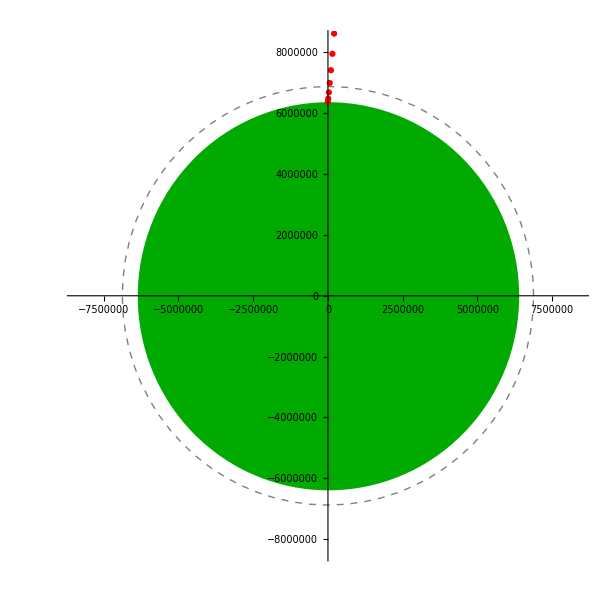

```mathematica
(*TwoStageOrbitIncremented[thrustx_,thrusty_,timeThrustApplied_,mass_,simulationRuntime_,initialHeight_]*)

TwoStageOrbitIncremented[10,200,40*60,10,10*3600,0]
```

```mathematica
lower=31700;
upper=31800;
TwoStageOrbitIncremented[#,1,1,1]&/@Range[lower,upper,(upper-lower)/5]
```

### Third Milestone

From there, we will model the same situations in 3D.

### Fourth Milestone

Finally, we will individually add in the components we were each responsible for researching (fuel consumption, air resistance).

### Old Content

```mathematica
(*velocitymodue[velocityx_, velocityy_, mass_]:= Module[{vx, vy, px, py, t, ag=-9.8, landingtime},
px=0;
py=0;
vx=velocityx;
vy=velocityy-ag t;
While[py≥0, (*stopping at the ground*)
px=vx t;
py=vy t + ag t^2;
landingtime= vy/ag;
Animate[Graphics[{px,py}, 
*)
```

```mathematica
thrustStage[initialPosx_,initialPosy_,thrustx_,thrusty_,timeThrustApplied_,mass_]:=Module[{force,acc,vel,pos,t,timeToGround,pathPlot},
(*set up the equations we will need. force and acc are constant but vel and pos are functions of t*)
force={thrustx,thrusty+mass*g};
acc=force/mass;
vel={0,0}+Integrate[acc,t]; (*No initial velocity*)
pos={initialPosx,initialPosy}+Integrate[vel,t];

(*set up the parametric plot*)
pathPlot=ParametricPlot[pos,{t,0,timeThrustApplied},PlotStyle->{Red, Dashed},AxesLabel->{"x Position","y Position"},PlotLabel->StringForm["Time thrust applied: `` seconds",timeThrustApplied]]
]
```

```mathematica
thrustStage[0,0,2,30,10,3]
```

```mathematica
freefallStage[initialPosx_,initialPosy_,initialVelx_,initialVely_,mass_]:=Module[{force,acc,vel,pos,t,timeToGround,pathPlot,animateTime,pathAnimation},
(*set up the equations we will need. force and acc are constant but vel and pos are functions of t*)
force={0,mass*g}; (*because the projectile is in freefall*) 
acc=force/mass;
vel={initialVelx,initialVely}+Integrate[acc,t];
pos={initialPosx,initialPosy}+Integrate[vel,t];

(*calculate the time it will take the projectile to reach the ground, where the y component of position is less than 0*)
timeToGround=t/.FindRoot[pos[[2]]==0,{t,100}];(*Current issue: how can we reliably find the positive root, not the negative one?*)

(*set up the parametric plot*)
pathPlot=ParametricPlot[pos,{t,0,timeToGround},PlotStyle->{Red, Dashed},AxesLabel->{"x Position","y Position"},PlotLabel->StringForm["Time to ground: `` seconds",timeToGround]]

(*We could try animating using the way described in that lab, by creating a list of frames and then combining them, instead of using the animate command directly*)

(*pathAnimation=Table[pathPlot,{animateTime,0,timeToGround,0.05}];
Animate[pathAnimation,{animateTime,0,timeToGround}]*)
]
```

```mathematica
freefallStage[10,10,6,5,50]
```

Module that produces plot of 2D motion and animation of projectile. I split posStageOne and posStageTwo so we can test animation

```mathematica
twoStageAnimated[thrustx_,thrusty_,timeThrustApplied_,mass_]:=Module[{g,force,acc,vel,posStageOne,posStageTwo,t,timeToGround,thrustPlot,freefallPlot},
(*define g*)
g=-9.8;

(*thrust stage*)
force={thrustx,thrusty+mass*g};
acc=force/mass;
vel={0,0}+Integrate[acc,t]; (*No initial velocity*)
posStageOne={0,0}+Integrate[vel,t];

(*set up the parametric plot for thrust stage*)
thrustPlot=ParametricPlot[posStageOne,{t,0,timeThrustApplied},PlotStyle->{Blue, Dashed}];

(*freefall stage*)
force={0,mass*g}; (*because the projectile is in freefall*) 
acc=force/mass;
vel=(vel/.t->timeThrustApplied)+Integrate[acc,t];
posStageTwo=(posStageOne/.t->timeThrustApplied)+Integrate[vel,t];

(*calculate the time it will take the projectile to reach the ground, where the y component of position is less than 0*)
timeToGround=t/.FindRoot[posStageTwo[[2]]==0,{t,100}];
(*Current issue: how can we reliably find the positive root, not the negative one?*)

(*set up the parametric plot*)
freefallPlot=ParametricPlot[posStageTwo,{t,0,timeToGround},PlotStyle->{Red, Dashed}];

(*Show the final plot*)
Show[{thrustPlot,freefallPlot},PlotRange->All,AxesLabel->{"x Position","y Position"},PlotLabel->StringForm["Time to ground: `` seconds",timeThrustApplied+timeToGround]]
]
```

```mathematica
twoStageAnimated[4,35,5,3]
```

### Notes

- Make acc, vel, and pos functions of [t_]. Do not use delayed set “:=”
- Change all instances of vel and pos within the code to vel[t] and pos[t]
- End the module with an Animate command
- To animate the two stage module, use an If statement to separate the animation depending on the value of t
- Separate out the two position variables as posThrustStage and posFreefallStage